```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/c++/seminar"];
```

```mathematica
Oscillator=Import["oscillator.dat"];
```

```mathematica
xList=Oscillator.{{1,0},{0,1},{0,0}};
```

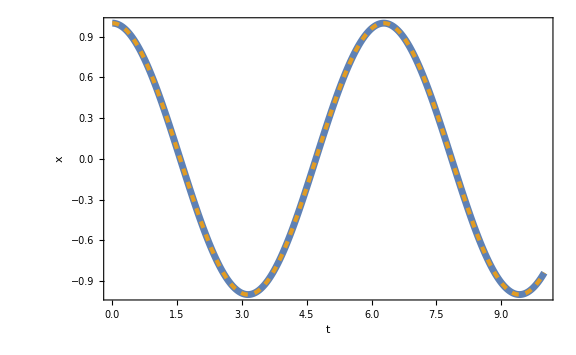

```mathematica
Show[ListPlot[xList,FrameLabel->{t,x},PlotLegends->Placed[LineLegend[{"num"},LegendMarkerSize->30],{0.87,0.8}],PlotStyle->AbsoluteThickness[5]],Plot[Cos[t],{t,0,10},PlotStyle->{Color[2],Dashed,AbsoluteThickness[3]},PlotLegends->Placed[LineLegend[{"cos t"},LegendMarkerSize->30],{0.87,0.8}]]]
```

```mathematica
Osc2=Import["2oscillator.dat"];
```

```mathematica
xList=Osc2.{{1,0},{0,1},{0,0},{0,0},{0,0}};
yList=Osc2.{{1,0},{0,0},{0,0},{0,1},{0,0}};
```

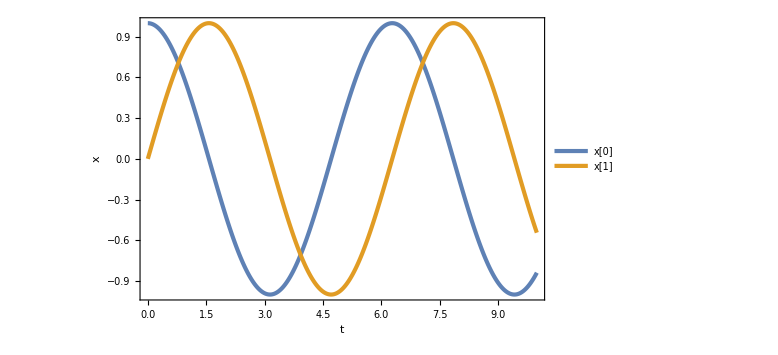

```mathematica
ListPlot[{xList,yList},FrameLabel->{t,x},PlotLegends->Placed[{"x[0]","x[1]"},{0.1,0.2}]]
```

```mathematica
DCbg=Import["double_chaotic_bg.dat"];
```

```mathematica
phiList=Map[{#[[6]],#[[2]]}&,DCbg];
psiList=Map[{#[[6]],#[[4]]}&,DCbg];
HList=Map[{#[[6]],#[[7]]}&,DCbg];
eList=Map[{#[[6]],#[[8]]}&,DCbg];
```

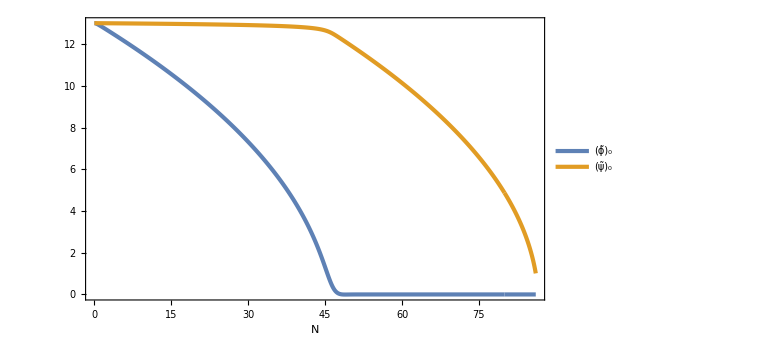

```mathematica
ListPlot[{phiList,psiList},FrameLabel->{N,None},PlotLegends->Placed[{Subscript[OverTilde[ϕ], 0],Subscript[OverTilde[ψ], 0]},{0.2,0.2}]]
```

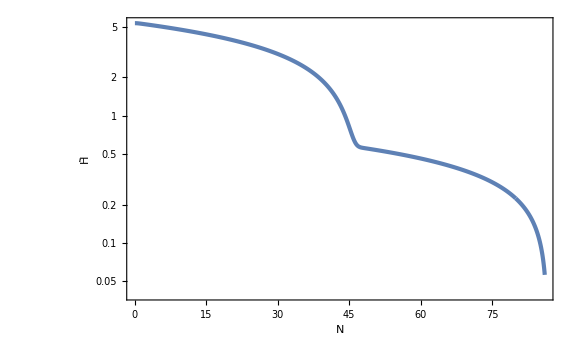

```mathematica
ListLogPlot[HList,FrameLabel->{N,OverTilde[H]}]
```

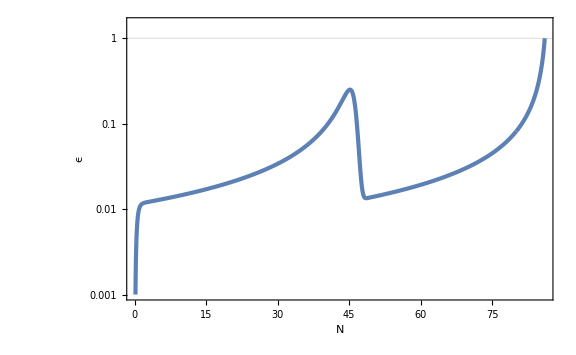

```mathematica
ListLogPlot[eList,FrameLabel->{N,ϵ},GridLines->{None,{1}},PlotRange->{0.001,1.5}]
```

```mathematica
DCptb=Import["double_chaotic_ptb.dat"];
```

```mathematica
phiList=Map[{#[[6]],#[[2]]}&,DCptb];
psiList=Map[{#[[6]],#[[4]]}&,DCptb];
HList=Map[{#[[6]],#[[7]]}&,DCptb];
eList=Map[{#[[6]],#[[8]]}&,DCptb];
calPR1List=Map[{#[[6]],#[[9]]}&,DCptb];
calPR2List=Map[{#[[6]],#[[10]]}&,DCptb];
calPR3List=Map[{#[[6]],#[[11]]}&,DCptb];
```

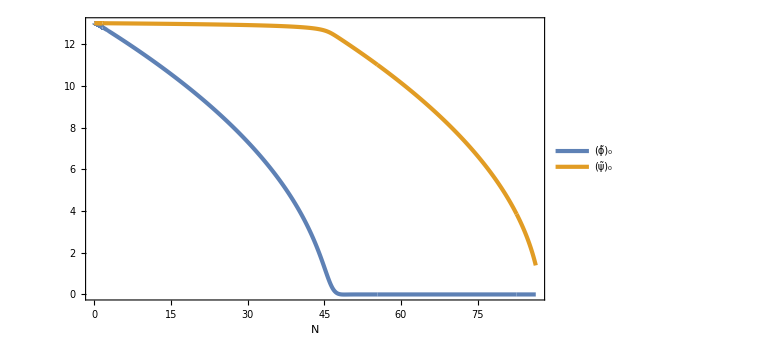

```mathematica
ListPlot[{phiList,psiList},FrameLabel->{N,None},PlotLegends->Placed[{Subscript[OverTilde[ϕ], 0],Subscript[OverTilde[ψ], 0]},{0.2,0.2}]]
```

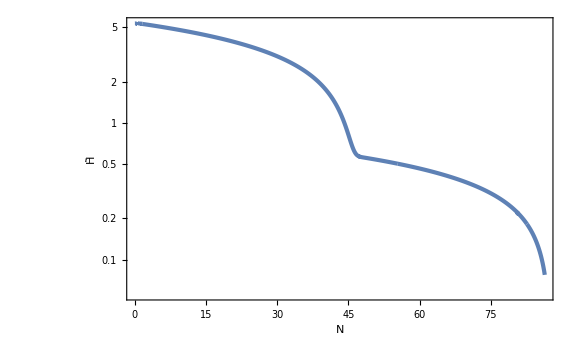

```mathematica
ListLogPlot[HList,FrameLabel->{N,OverTilde[H]}]
```

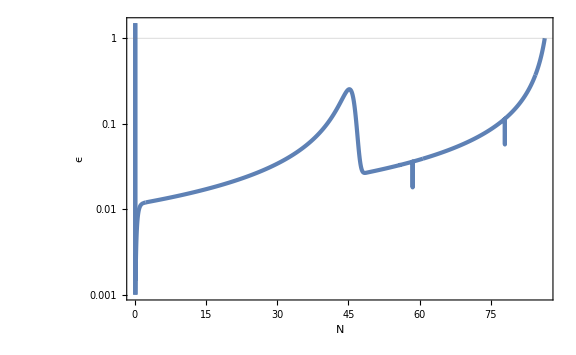

```mathematica
ListLogPlot[eList,FrameLabel->{N,ϵ},GridLines->{None,{1}},PlotRange->{0.001,1.5}]
```

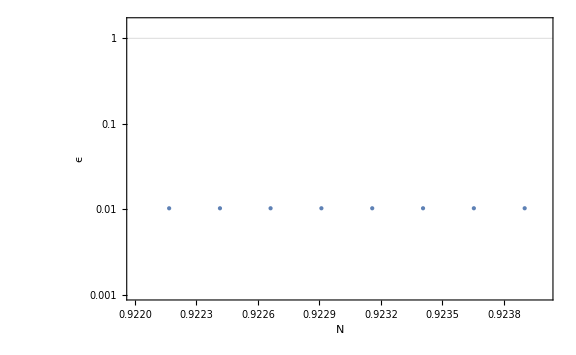

```mathematica
ListLogPlot[eList,FrameLabel->{N,ϵ},GridLines->{None,{1}},PlotRange->{{0.922,0.924},{0.001,1.5}},Joined->False,PlotStyle->Directive[PointSize->Large]]
```

```mathematica
Select[DCptb,0.922<#[[6]]<0.924&]
```

{{0.173009,12.9072,-0.759414,12.9989,-0.0094168,0.922179,5.31128,0.010225,4.43697×10^-6,4.56848×10^-6,4.64759×10^-6},{0.173056,12.9072,-0.759452,12.9989,-0.00941728,0.922427,5.31127,0.010226,4.43519×10^-6,4.56605×10^-6,4.64411×10^-6},{0.173103,12.9071,-0.759489,12.9989,-0.00941777,0.922674,5.31126,0.0102271,4.43341×10^-6,4.56361×10^-6,4.64062×10^-6},{0.173149,12.9071,-0.759527,12.9989,-0.00941825,0.922922,5.31124,0.0102282,4.43163×10^-6,4.56115×10^-6,4.63713×10^-6},{0.173196,12.907,-0.759564,12.9989,-0.00941874,0.92317,5.31123,0.0102292,4.42985×10^-6,4.55867×10^-6,4.63362×10^-6},{0.173242,12.907,-0.759602,12.9988,-0.00941922,0.923418,5.31122,0.0102303,4.42806×10^-6,4.55618×10^-6,4.63011×10^-6},{0.173289,12.907,-0.759639,12.9988,-0.00941971,0.923666,5.3112,0.0102313,4.42628×10^-6,4.55367×10^-6,4.62659×10^-6},{0.173336,12.9069,-0.759677,12.9988,-0.00942019,0.923914,5.31119,0.0102324,4.42449×10^-6,4.55115×10^-6,4.62306×10^-6}}

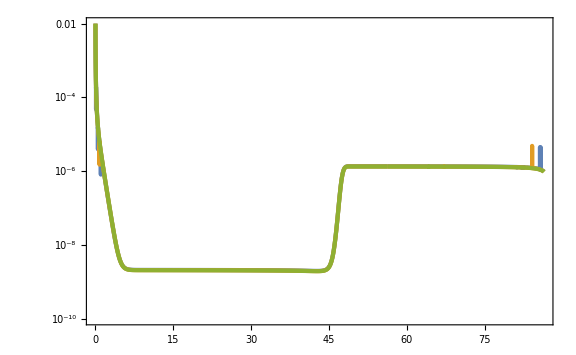

```mathematica
ListLogPlot[{calPR1List,calPR2List,calPR3List},PlotRange->{10^-10,0.01}]
```

```mathematica
Last[calPR1List][[2]]
Last[calPR2List][[2]]
Last[calPR3List][[2]]
```

9.83287×10^-7

9.69321×10^-7

9.6538×10^-7